# Optical pumping effect in Imaging

Here we go

```mathematica
ClearAll["Global`*"]
```

Optical Bloch equation is

```mathematica
equns={
w'[t]==-Ω v[t]+(1+p)Γ ρ[t],
u'[t]==Δ v[t]-q Γ u[t],
v'[t]==Ω w[t]-Δ u[t]-q Γ v[t],
ρ'[t]==Ω/2 v[t]-Γ ρ[t],
w[0]==1,u[0]==0,v[0]==0,ρ[0]==0};
```

```mathematica
ASol=First@DSolve[equns,{w[t],u[t],v[t],ρ[t]},t]
```

{u[t]→2 Δ Ω RootSum[8 q Γ^2 Ω^2-8 p q Γ^2 Ω^2+8 q^2 Γ^3 #1+8 Γ Δ^2 #1+4 Γ Ω^2 #1-4 p Γ Ω^2 #1+8 q Γ Ω^2 #1+8 q Γ^2 #1^2+4 q^2 Γ^2 #1^2+4 Δ^2 #1^2+4 Ω^2 #1^2+2 Γ #1^3+4 q Γ #1^3+#1^4&,(2 ⅇ^((t #1)/2) Γ+ⅇ^((t #1)/2) #1)/(4 q^2 Γ^3+4 Γ Δ^2+2 Γ Ω^2-2 p Γ Ω^2+4 q Γ Ω^2+8 q Γ^2 #1+4 q^2 Γ^2 #1+4 Δ^2 #1+4 Ω^2 #1+3 Γ #1^2+6 q Γ #1^2+2 #1^3)&],v[t]→Ω RootSum[8 q Γ^2 Ω^2-8 p q Γ^2 Ω^2+8 q^2 Γ^3 #1+8 Γ Δ^2 #1+4 Γ Ω^2 #1-4 p Γ Ω^2 #1+8 q Γ Ω^2 #1+8 q Γ^2 #1^2+4 q^2 Γ^2 #1^2+4 Δ^2 #1^2+4 Ω^2 #1^2+2 Γ #1^3+4 q Γ #1^3+#1^4&,(4 ⅇ^((t #1)/2) q Γ^2+2 ⅇ^((t #1)/2) Γ #1+2 ⅇ^((t #1)/2) q Γ #1+ⅇ^((t #1)/2) #1^2)/(4 q^2 Γ^3+4 Γ Δ^2+2 Γ Ω^2-2 p Γ Ω^2+4 q Γ Ω^2+8 q Γ^2 #1+4 q^2 Γ^2 #1+4 Δ^2 #1+4 Ω^2 #1+3 Γ #1^2+6 q Γ #1^2+2 #1^3)&],w[t]→1/2 RootSum[8 q Γ^2 Ω^2-8 p q Γ^2 Ω^2+8 q^2 Γ^3 #1+8 Γ Δ^2 #1+4 Γ Ω^2 #1-4 p Γ Ω^2 #1+8 q Γ Ω^2 #1+8 q Γ^2 #1^2+4 q^2 Γ^2 #1^2+4 Δ^2 #1^2+4 Ω^2 #1^2+2 Γ #1^3+4 q Γ #1^3+#1^4&,(8 ⅇ^((t #1)/2) q^2 Γ^3+8 ⅇ^((t #1)/2) Γ Δ^2+8 ⅇ^((t #1)/2) q Γ^2 #1+4 ⅇ^((t #1)/2) q^2 Γ^2 #1+4 ⅇ^((t #1)/2) Δ^2 #1+2 ⅇ^((t #1)/2) Γ #1^2+4 ⅇ^((t #1)/2) q Γ #1^2+ⅇ^((t #1)/2) #1^3)/(4 q^2 Γ^3+4 Γ Δ^2+2 Γ Ω^2-2 p Γ Ω^2+4 q Γ Ω^2+8 q Γ^2 #1+4 q^2 Γ^2 #1+4 Δ^2 #1+4 Ω^2 #1+3 Γ #1^2+6 q Γ #1^2+2 #1^3)&],ρ[t]→Ω^2 RootSum[8 q Γ^2 Ω^2-8 p q Γ^2 Ω^2+8 q^2 Γ^3 #1+8 Γ Δ^2 #1+4 Γ Ω^2 #1-4 p Γ Ω^2 #1+8 q Γ Ω^2 #1+8 q Γ^2 #1^2+4 q^2 Γ^2 #1^2+4 Δ^2 #1^2+4 Ω^2 #1^2+2 Γ #1^3+4 q Γ #1^3+#1^4&,(2 ⅇ^((t #1)/2) q Γ+ⅇ^((t #1)/2) #1)/(4 q^2 Γ^3+4 Γ Δ^2+2 Γ Ω^2-2 p Γ Ω^2+4 q Γ Ω^2+8 q Γ^2 #1+4 q^2 Γ^2 #1+4 Δ^2 #1+4 Ω^2 #1+3 Γ #1^2+6 q Γ #1^2+2 #1^3)&]}

```mathematica
ngava[T_]:=1/T NIntegrate[(w[t]+ρ[t])/.Sol,{t,0,T}];
```

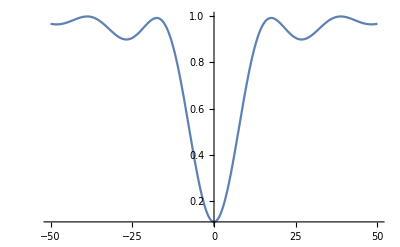

```mathematica
Plot[Evaluate[(w[t]+ρ[t])/.ASol//.{Δ->δ,Γ->1,Ω->10,p->1,q->0.5,t->0.314}],{δ,-50,50},PlotRange->All]
```

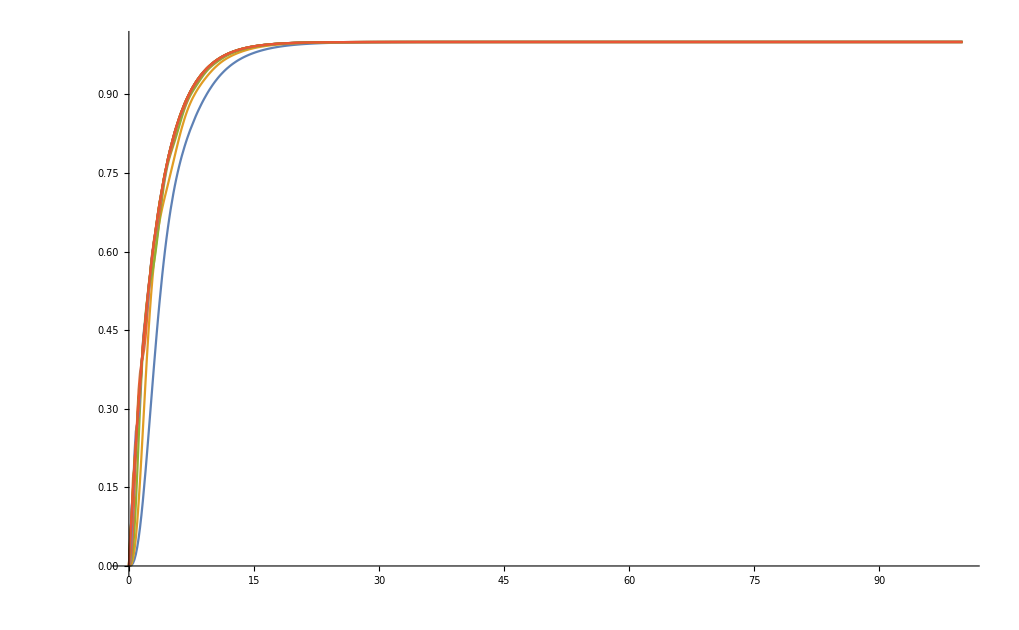

```mathematica
Plot[Evaluate@Table[(1-w[t]-2ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->10^power,p->0.36,q->0.5},{power,-0,2,0.2}],{t,0,100},PlotRange->All,PlotPoints->10]
```

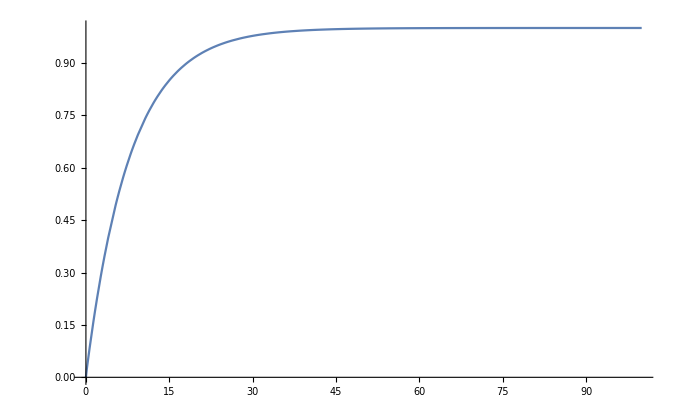

```mathematica
Plot[Evaluate@Table[(1-w[t]-2ρ[t])/.ASol//.{t->τ/0.0277,Δ->det,Γ->1,Ω->1.64,p->0.36,q->0.5},{det,11,11,1}],{τ,0,100},PlotRange->All, PlotPoints->10]
```

```mathematica
FindFit
```

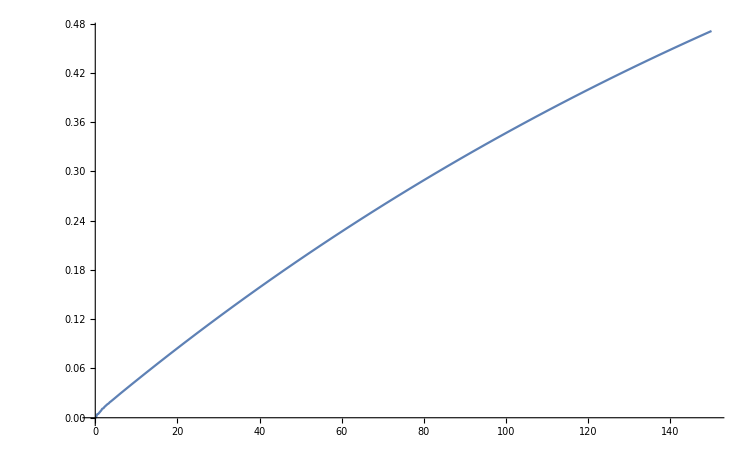

```mathematica
Plot[(1-w[t]-2ρ[t])/.ASol//.{Δ->10,Γ->1,Ω->1.64,p->0.36,q->0.5},{t,0,150},PlotRange->All]
```

```mathematica
Chop[1/10 NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->1,p->0.36,q->0.5},{t,0,0.1}]]
```

0.00999185

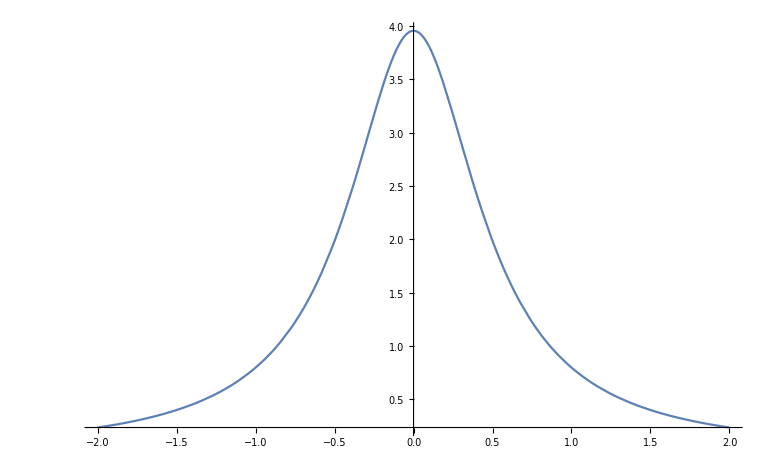

```mathematica
Plot[1/(0.25+δ^2)Chop[1/10 NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->δ,Γ->1,Ω->0.1,p->0.85,q->0.5},{t,0,10}]],{δ,-2,2},PlotPoints->5,PlotRange->All]
```

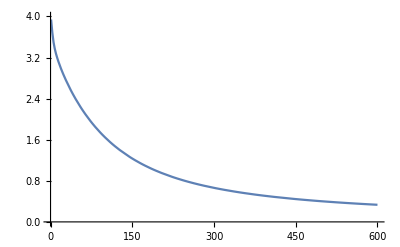

```mathematica
Plot[1/(0.25+0^2)Chop[1/T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->0.5,p->0.9,q->0.5},{t,0,T}]],{T,1,600},PlotPoints->5,PlotRange->{0,4}]
```

```mathematica
Plot3D[1/(0.25(1+(10^ω)^2))Chop[1/10^T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->10^ω,p->0.001,q->0.5},{t,0,10^T}]],{ω,-2,2},{T,-2,3},PlotPoints->30,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(0.25(1+(10^ω)^2))Chop[1/10^T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->10^ω,p->1,q->0.5},{t,0,10^T}]],{ω,-2,2},{T,-2,3},PlotPoints->30,PlotRange->All]
```

-Graphics3D-

```mathematica
Show[%29,ViewPoint->{0,-∞,0},ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[1/(0.25(1+(10^ω)^2))Chop[1/10^T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->10^ω,p->0.85,q->0.5},{t,0,10^T}]],{ω,-2,2},{T,-2,3},PlotPoints->30,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/0.25 Chop[1/10^T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->10^ω,p->0.85,q->0.5},{t,0,10^T}]],{ω,-2,2},{T,-2,3},PlotPoints->50,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/0.25 Chop[1/10^T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->0,Γ->1,Ω->10^ω,p->0.85,q->0.5},{t,0,10^T}]],{ω,-2,2},{T,-2,3},PlotPoints->100,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(0.25+δ^2)Chop[1/T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->δ,Γ->1,Ω->1,p->0.85,q->0.5},{t,0,T}]],{δ,-2,2},{T,0.1,600},PlotPoints->50,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(0.25+δ^2)Chop[1/T NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->δ,Γ->1,Ω->0.1,p->0.85,q->0.5},{t,0,T}]],{δ,-2,2},{T,0.1,600},PlotPoints->50,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(0.25+δ^2)Chop[1/300 NIntegrate[(w[t]+ρ[t])/.ASol//.{Δ->δ,Γ->1,Ω->10^ω,p->0.85,q->0.5},{t,0,300}]],{δ,-2,2},{ω,-2,2},PlotPoints->30,PlotRange->All]
```

-Graphics3D-

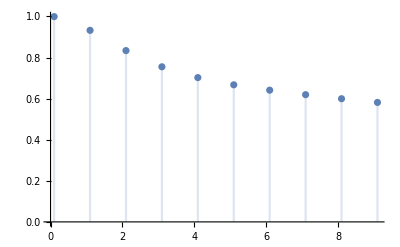

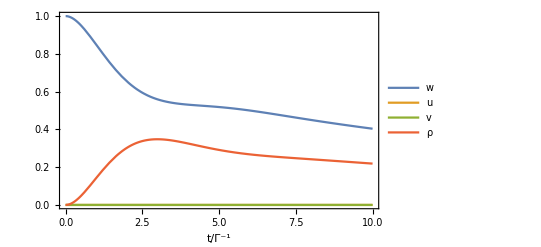

```mathematica
τ=0.1*10^2;
Sol=First@NDSolve[equns/.{Δ->0,Γ->1,Ω->1,p->0.85,q->0.5},{w,u,v,ρ},{t,0,τ}];
ngava[T_]:=1/T NIntegrate[(w[t]+ρ[t])/.Sol,{t,0,T}];
DiscretePlot[ngava[t],{t,0.1,τ,1},PlotRange->{0,1}]
Plot[Evaluate[{w[t]+ρ[t],0u[t],0v[t],ρ[t]}/.Sol], {t, 0, τ}, PlotRange->All,ImageSize->Scaled[0.8],Frame->True,FrameLabel->{Style["t/Γ^-1",FontFamily->"Goudy Old Style",FontSize->16],Style["",FontFamily->"Goudy Old Style",FontSize->16]},PlotLegends->{"w","u","v","ρ"}]
```

```mathematica
0.167*1.57
```

0.26219

```mathematica
4.17*10^7 √1.67
```

5.38883×10^7

```mathematica
1/6.066
```

0.164853

```mathematica
164ns
```